# WL—Training General 1

## Getting information

Use ? and ?? to get information about a Symbol

? uses the function Information

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

```mathematica
??Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]:={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Use Options[symbol] to find the default values for the Options to a Symbol (function)

```mathematica
Options[Graph]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSelectable→Automatic,DirectedEdges→Automatic,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→None,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,Epilog→{},FormatType→TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme→Automatic,Prolog→{},Properties→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{},VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→None,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic}

FilterRules can be used to find subsets of Options based on patterns

```mathematica
FilterRules[Options[Graph],Except[Options[Graphics]]]
```

{DirectedEdges→Automatic,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→None,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,PerformanceGoal:>$PerformanceGoal,PlotTheme→Automatic,Properties→{},VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→None,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic}

Use Names to find symbols

Very helpful when you can remember the full name, or when you want to know all variations

```mathematica
Names["*Plot*"]
```

{AnatomyPlot3D,ArrayPlot,AudioPlot,BodePlot,ChromaticityPlot,ChromaticityPlot3D,CommunityGraphPlot,ContourPlot,ContourPlot3D,DateListLogPlot,DateListPlot,DateListStepPlot,DensityPlot,DensityPlot3D,DiscretePlot,DiscretePlot3D,FeatureSpacePlot,GeoListPlot,GeoRegionValuePlot,GraphPlot,GraphPlot3D,JuliaSetPlot,LayeredGraphPlot,LineIntegralConvolutionPlot,ListContourPlot,ListContourPlot3D,ListCurvePathPlot,ListDensityPlot,ListDensityPlot3D,ListLineIntegralConvolutionPlot,ListLinePlot,ListLogLinearPlot,ListLogLogPlot,ListLogPlot,ListPlot,ListPlot3D,ListPointPlot3D,ListPolarPlot,ListSliceContourPlot3D,ListSliceDensityPlot3D,ListSliceVectorPlot3D,ListStepPlot,ListStreamDensityPlot,ListStreamPlot,ListSurfacePlot3D,ListVectorDensityPlot,ListVectorPlot,ListVectorPlot3D,LogLinearPlot,LogLogPlot,LogPlot,MandelbrotSetPlot,MatrixPlot,MaxPlotPoints,NicholsPlot,NumberLinePlot,NyquistPlot,ParametricPlot,ParametricPlot3D,Plot,Plot3D,Plot3Matrix,PlotDivision,PlotJoined,PlotLabel,PlotLabels,PlotLayout,PlotLegends,PlotMarkers,PlotPoints,PlotRange,PlotRangeClipping,PlotRangeClipPlanesStyle,PlotRangePadding,PlotRegion,PlotStyle,PlotTheme,PolarPlot,ProbabilityPlot,ProbabilityScalePlot,QuantilePlot,ReactionNetworkPlot,RegionPlot,RegionPlot3D,ReliefPlot,RevolutionPlot3D,RootLocusPlot,RulePlot,SingularValuePlot,SliceContourPlot3D,SliceDensityPlot3D,SliceVectorPlot3D,SphericalPlot3D,StreamDensityPlot,StreamPlot,TimelinePlot,TreePlot,VectorDensityPlot,VectorPlot,VectorPlot3D,WaveletImagePlot,WaveletListPlot,WaveletMatrixPlot,$PlotTheme}

```mathematica
AnatomyPlot3D
```

```mathematica
"AnatomyPlot3D"
```

A list of Strings is returned

## Assigning values to Symbols (aka OwnValues)

= is the infix notation for Set

:= is the infix notation for SetDelayed

The left hand side (lhs) is a Symbol

The transformation rule is stored in the OwnValues for the symbol

```mathematica
x=1;
y:=2+x;
```

```mathematica
OwnValues[x]
```

{HoldPattern[x]:>1}

```mathematica
OwnValues[y]
```

{HoldPattern[y]:>2+x}

## Defining functions (aka DownValues)

Functions are most often defined with SetDelayed to create DownValues

SetDelayed is generally used

The lhs is a normal expression, that is, it has a Head

They are transformation rules (productions): pattern on lhs, operation or output on rhs

The transformation rules are stored in the DownValues for the symbol that is the head of the lhs

```mathematica
z[a_]:=a^2
```

```mathematica
DownValues[z]
```

{HoldPattern[z[a_]]:>a^2}

```mathematica
fib[1]:=1
fib[2]:=1
fib[n_Integer?Positive]:=fib[n-1]+fib[n-2]
```

```mathematica
DownValues[fib]//Column
```

HoldPattern[fib[1]]:>1
HoldPattern[fib[2]]:>1
HoldPattern[fib[n_]]:>fib[n-1]+fib[n-2]

Mathematica will ordered the list of DownValues from most specific to most general

Sometimes you may need to manually reorder the list because the specificity is undecidable

Even if you have only only one definition for a function, use a pattern in the lhs instead of just input_

It self-defines the structure of the data that your function expects as input

It will also avoid GIGO if you make a mistake using the function

```mathematica
fib[4]
```

3

```mathematica
fib[4.5]
```

$RecursionLimit::reclim2: Recursion depth of 512 exceeded during evaluation of fib[-505.5-1].

Hold[fib[4.5-1]+fib[4.5-2]]

```mathematica
$RecursionLimit
```

512

```mathematica
$RecursionLimit=1000000
```

1000000

### Patterns

Pattern expressions specify the arguments

_ ⟶ any expression (Blank[])

_head ⟶ any expression with Head head (Blank[head])

s_ ⟶ any expression with the name s (Pattern[s,Blank[]])

Patterns can also represent sequences

__ ⟶ any sequence of one or more expressions (BlankSequence[])

___ ⟶ any sequence of zero or more expressions (BlankNullSequence[])

Use MatchQ to test an expression against a pattern

```mathematica
MatchQ[{1,2,3,4,5},{__?OddQ}]
```

False

```mathematica
MatchQ[{1,3,5},{__?OddQ}]
```

True

### Tests

Use ? to require a test to be met by the expression

Good for predicates

### Conditions

Use /; to require a condition to be met by the expression

good when multiple parts of the pattern are involved

```mathematica
MatchQ[{1,2,3,4,5},{i_,j_,___}/;i<j]
```

True

```mathematica
MatchQ[{5,4,3,2,1},{i_,j_,___}/;i<j]
```

False

```mathematica
MatchQ[{a,b,c,d,e},{i_,j_,___}/;i<j]
```

False

```mathematica
Sort[{c,d,b,a,e}]
```

{a,b,c,d,e}

### Repetition

.. ⟶ a pattern repeated one or more times (Repeated)

... ⟶ a pattern repeated zero or more times (RepeatedNull)

```mathematica
MatchQ[{3,3,3},{(x_?OddQ)...}]
```

True

```mathematica
MatchQ[{},{(x_?OddQ)...}]
```

True

## Starting anew—removing definitions

Clear removes the OwnValues and DownValues assigned to a symbol

ClearAll also removes Attributes, FormatValues

```mathematica
ClearAll[f]
f[x_]:=...
```

## Function

### Basics

WL permits functions without formal names: pure, or anonymous functions

They are often used in “one-liners”

Syntax: # represents the argument, & indicates the end of the body of the function

```mathematica
#^2&/@{1,2,3,4}
```

{1,4,9,16}

```mathematica
Slot[1]->#1
```

```mathematica
#age
```

```mathematica
3(#1+#2)&@@@{{1,2},{3,4},{a,b}}
```

{9,21,3 (a+b)}

```mathematica
Apply[3(#1+#2)&,{{1,2},{3,4},{a,b}},{1}]
```

{9,21,3 (a+b)}

### Nested use

A pure function can be used within another pure function

Let’s make a function that sorts a list of instructors by their last name, which is the second element of the instructor data object

```mathematica
instructors={
{"Kyle","Keane","remote"},
{"Xavier","Roy","remote"},
{"Vitaliy","Kaurov","remote"},
{"Kevin","Daily","local"},
{"Riccardo","Di Virgilio","remote"},
{"Carlo","Barbieri","remote"}
};
```

```mathematica
SortBy[#,#⟦2⟧&]&[instructors]//Column
```

{Carlo,Barbieri,remote}
{Kevin,Daily,local}
{Riccardo,Di Virgilio,remote}
{Vitaliy,Kaurov,remote}
{Kyle,Keane,remote}
{Xavier,Roy,remote}

```mathematica
Function[{instructor},SortBy[instructor,#⟦2⟧&]][instructors]//Column
```

{Carlo,Barbieri,remote}
{Kevin,Daily,local}
{Riccardo,Di Virgilio,remote}
{Vitaliy,Kaurov,remote}
{Kyle,Keane,remote}
{Xavier,Roy,remote}

```mathematica
[[2]]⟦⟧
```

## Options

Options are specified as Rule (->) or RuleDelayed (:>)

They come after all the other arguments

Default values are defined with Options or SetOptions

```mathematica
Options[f]={maxRange->5,minValue->-2}
```

{maxRange→5,minValue→-2}

```mathematica
SetOptions[f,minValue->0]
```

{maxRange→5,minValue→0}

```mathematica
??f
```

Global`f

Options[f]={maxRange→5,minValue→-2}

OptionsPattern, OptionValue, FilterRules

```mathematica
f[x_,OptionsPattern[]]:=Module[{a},a=x^2;a+OptionValue[minValue]]
```

```mathematica
f[3]
```

9

```mathematica
f[3,minValue->6]
```

15

```mathematica
f[x_,opts:OptionsPattern[]]:=Module[{a},a=x^2;Plot[a+OptionValue[minValue],opts]
]
```

```mathematica
f[x_,opts:OptionsPattern[]]:=Module[{a},a=x^2;Plot[a+OptionValue[minValue],FilterRules[{opts},Options[Plot]]]
]
```

## Attributes

Attributes modify the behavior of the evaluation process for a symbol

They can be thought of as properties

They are specified with Attributes or SetAttributes

### Listable

Allows the head of an expression to be threaded over arguments that are Lists

Kind of like “vectoring” a function

```mathematica
sq[x_]:=g[x]
```

```mathematica
g[x_]:=x^2
```

```mathematica
sq[3]
```

g[3]

```mathematica
sq[{1,2,3}]
```

g[{1,2,3}]

```mathematica
sq[{1,2,3}]
```

```mathematica
SetAttributes[sq,Listable]
```

```mathematica
sq[{1,2,3}]
```

{g[1],g[2],g[3]}

```mathematica
sq[{1,2,3}]
```

{1,4,9}

```mathematica
Attributes[sq]
```

{Listable}

### Flat

Like the associative property of algebra

```mathematica
ClearAll[f]
f[f[x]]
```

f[f[x]]

```mathematica
SetAttributes[f,Flat]
```

```mathematica
f[f[4]]
```

f[4]

### Orderless

Like the commutative property of algebra

### HoldAll, HoldFirst, HoldRest

The arguments are not evaluated before the transformation rule is applied

## Scoping

Scoping constructs localize the use of a symbol

### Functionally

Two arguments: list of local symbols and a body

They can be nested

#### Module

New, unique local symbols are generated and used

The values of the symbols can be modified

```mathematica
a=12
```

12

```mathematica
Module[{a=1,b},b=3;a+b]
```

4

```mathematica
a
```

12

```mathematica
Module[{a,b},{a,b}]
```

{a$8762,b$8762}

#### Block

Existing symbols are saved, and then restored

Useful for temporarily modifying a symbol, e.g., $Path

```mathematica
a=12
```

12

```mathematica
Block[{a=1,b=3},a+b]
```

4

```mathematica
a
```

12

#### With

The values of the local symbols are constant

The instances of the local symbols in the body are replaced by their values before the body is evaluated

```mathematica
With[{x=5},a+x]
```

5+a

```mathematica
With[{x=5},x=x+2;a+x]
```

Set::setraw: Cannot assign to raw object 5.

5+a

### Procedurally

Contexts

BeginPackage["myProject`"]

(* all the usage and error messages *)

Begin["`Private`"]

(* all my code *)

End[] (* ends the Private` context *)

EndPackage[] (* ends the myPackage` context ()

Analogous to moving up and down a directory hierarchy

Used in packages—Ian Johnson’s talk next week

## Conditional evaluation

### If

One Boolean test with 1, 2, or 3 branches

```mathematica
If[x,
(* x is True *)y=4,
(* x is False *)y=5,
(* x is neither True nor False *) y=0
]
```

### Which

Multiple Boolean test and branch pairs

```mathematica
Which[a==3,z,a==4,q,True,0]
```

0

### Switch

One expression and multiple pattern and branch pairs

```mathematica
Switch[x,{_},x,{_,_},w,_,y]
```

y

## Levels

Expressions can be nested, and ∴ have a depth

Functions and rules can be applied to the whole expression or to the parts at specific depths, or levels

A level specification is a single level or a continuous range of levels

Levels can be specified from the top or the bottom of an expression

## Select, Cases, DeleteCases

Sometime you want elements from a list based on their value

```mathematica
Select[{1,2,3,4,5},OddQ]
```

{1,3,5}

```mathematica
Cases[{1,2,3,4,5},_?OddQ]
```

{1,3,5}

```mathematica
DeleteCases[{1,2,3,4,5},_?OddQ]
```

{2,4}

```mathematica
Position[{1,2,3,4,5},_?OddQ,{1}]
```

{{1},{3},{5}}

## Recursion

Base case(s) and recursion rule

Often used for traversing hierarchical (nested) structures, such as trees

```mathematica
tree={"a",{{"b",{{"c"},{"d"}}},{"e"}}};
```

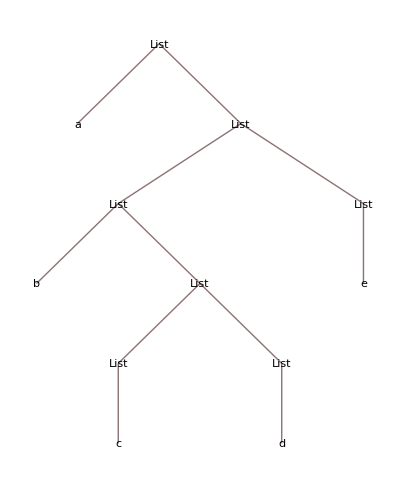

```mathematica
TreeForm[tree]
```

```mathematica
dfsPost[{leaf_}]:={leaf}
dfsPost[{root_,branches:{__}}]:=Append[Join@@dfsPost/@branches,root]
```

```mathematica
dfsPost[tree]
```

{c,d,b,e,a}